# Sensitivity Calculations

This notebook contains calculations relating to the sensitivity section of the paper. The notebook sections follow the order of subsections in the paper

## Sensitivity at equilibrium

```mathematica
Clear["Global`*"]
```

### Define state weights. Take “empty” state (state 2) to have weight equal to 1

```mathematica
B = 1/(kb*T);
```

```mathematica
ec = mu - kb*T*Log[c];
```

```mathematica
w2 = 1;
```

```mathematica
w1 = FullSimplify[Exp[-B*ec]]
```

c ⅇ^(-mu/(kb T))

```mathematica
w3 = Exp[-B*en];
```

```mathematica
w4 = Simplify[Exp[-B*(en+enc+ec)]]
```

c ⅇ^(-(en+enc+mu)/(kb T))

### Define probability of being in the on state

```mathematica
pOn=FullSimplify[(w3+w4)/(w1+w2+w3+w4) ]
```

(c+ⅇ^((enc+mu)/(kb T)))/(c+c ⅇ^((en+enc)/(kb T))+ⅇ^((enc+mu)/(kb T))+ⅇ^((en+enc+mu)/(kb T)))

### Simplify by substituting weight variables for exponentiated energies

```mathematica
pOnSimp =FullSimplify[pOn /.{ⅇ^(enc/(kb T))-> 1/ws,ⅇ^((enc+mu)/(kb T))-> 1/ws * 1/wc,ⅇ^((en+enc)/(kb T))->1/wm*1/ws,ⅇ^((en+enc+mu)/(kb T))->1/wm*1/ws*1/wc,ⅇ^(en/(kb T))-> 1/wm}]
```

(wm+c wc wm ws)/(1+c wc+wm+c wc wm ws)

### Calculate sharpness and maximize wrpt state energies

```mathematica
sOnFull = FullSimplify[D[pOn,c]]
```

-(ⅇ^((en+enc+mu)/(kb T)) (-1+ⅇ^(enc/(kb T))))/((c+c ⅇ^((en+enc)/(kb T))+ⅇ^((enc+mu)/(kb T))+ⅇ^((en+enc+mu)/(kb T)))^2)

```mathematica
sOnSimp = FullSimplify[D[pOnSimp ,c]]
```

(wc wm (-1+ws))/(1+wm+c (wc+wc wm ws))^2

```mathematica
maxSol = NMaximize[{sOnSimp/.c->1,wm>0,wc>0,ws>0},{wm,wc,ws}]
```

{0.249092,{wm→0.00180934,wc→0.00180934,ws→303635.}}

So we see that the sharpness maximization (or minimization) criterion is that a*c = b = w^-(1/2)

### Simplify further to understand constraints on magnitudes of a,b, and w

```mathematica
sOnSimpSimp = FullSimplify[sOnSimp  /. {wc->wm/c,ws->1/wm^2}]
```

(1-wm)/(4 c+4 c wm)

So for activation  (s>0), sharpness in maximized when ac,b <<1, which implies that w>>1

## Large energy barrier implies slow fluctuation timescales

### Plot sharpness vs weight of 01 and 10 states

```mathematica
sOnFun[wm_] = sOnSimpSimp/.c->1;
```

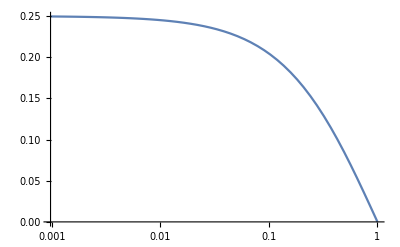

```mathematica
LogLinearPlot[sOnFun[wm],{wm,0,1}]
```

### Define simplified transition matrix

```mathematica
Qeq = ({{-b4-b1*wm*ws, b4 c wc, 0, b1}, {b4, -b4 c wc-k1 wm, k1, 0}, {0, k1 wm, -c*wc*ws*k4-k1, k4}, {b1*wm*ws, 0, c*wc*ws*k4, -k4-b1}});
```

```mathematica
MatrixForm[Qeq]
```

(-b4-b1 wm ws | b4 c wc | 0 | b1
b4 | -b4 c wc-k1 wm | k1 | 0
0 | k1 wm | -k1-c k4 wc ws | k4
b1 wm ws | 0 | c k4 wc ws | -b1-k4)

```mathematica
Total[Qeq]
```

{0,0,0,0}

```mathematica
eigVectorsEq = Eigenvectors[Qeq];
```

```mathematica
ssVecEq = eigVectorsEq[[1]] / Total[eigVectorsEq[[1]]];
```

```mathematica
Zeq = Denominator[ssVecEq[[2]]];
```

c wc wm (1+1/(c wc ws)+1/(wm ws)+1/(c wc wm ws)) ws

```mathematica
pdRateEq = FullSimplify[ssVecEq[[3]]+ssVecEq[[4]]]
```

(wm+c wc wm ws)/(1+c wc+wm+c wc wm ws)

```mathematica
sensitivityEq = FullSimplify[D[pdRateEq,c]]
```

(wc wm (-1+ws))/(1+wm+c (wc+wc wm ws))^2

```mathematica
sensitivityEqSimp = FullSimplify[sensitivityEq /.c->1/.{wm->wc,ws->(wc)^(-2)}]
```

(1-wc)/(4+4 wc)

```mathematica
NMaximize[{sensitivityEqSimp,b4>0,b2>0,k1>0,k3>0,wc>0}, {b4,b2,k1,k3,wc}]
```

{0.25,{b4→0.,b2→0.,k1→0.,k3→0.,wc→0.}}

### Calculate average cycle time (J+ + J-)

Define transition matrix for expanded diagram

```mathematica
Jp = FullSimplify[Qeq[[1,2]]*Qeq[[2,3]]*Qeq[[3,4]]*Qeq[[4,1]] / Zeq]
```

(b1 b4 c k1 k4 wc wm ws)/(1+wm+c (wc+wc wm ws))

```mathematica
Jm = FullSimplify[Qeq[[2,1]]*Qeq[[3,2]]*Qeq[[4,3]]*Qeq[[1,4]] / Zeq]
```

(b1 b4 c k1 k4 wc wm ws)/(1+wm+c (wc+wc wm ws))

```mathematica
Jt = FullSimplify[Jp+Jm]
```

(2 b1 b4 c k1 k4 wc wm ws)/(1+wm+c (wc+wc wm ws))

```mathematica
J = FullSimplify[Jp-Jm]
```

0

Apply sharpness maximization conditions

```mathematica
JtMax = Limit[Jt /. c->1 /. {wm ->wc,ws->1/wc^2},wc->0]
```

b1 b4 k1 k4

Generally, we might expect that k1,b4>>k4,b1; however this does not necessarily need to be the case

## Preferred cycle direction for activator network

```mathematica
tauOnSimp = FullSimplify[ET24val /.{k3->k,k1->r,b2->r,b4->k} ]
```

(k r (1+c wc+wm)+c k k4 wc (1+c wc) ws+b1 wm ws (r+r wm+c k4 wc ws))/(c wc wm ws (k (b1+k4) r+b1 k4 (c k wc+r wm) ws))

```mathematica
tauOffSimp = FullSimplify[ET42val /.{k3->k,k1->r,b2->r,b4->k} ]
```

(k (k4+r+c k4 wc ws)+b1 (r+r wm ws+k4 ws (c wc+wm+c wc wm ws)))/(k (b1+k4) r+b1 k4 (c k wc+r wm) ws)

```mathematica
pdSimp =FullSimplify[ET42val/ (ET42val +ET24val)/.{k3->k,k1->r,b2->r,b4->k} ]
```

(c wc wm ws (k (k4+r+c k4 wc ws)+b1 (r+r wm ws+k4 ws (c wc+wm+c wc wm ws))))/((r+c k4 wc ws) (k+b1 wm ws) (1+wm+c (wc+wc wm ws)))

## Nonequilibrium approach

### Define transition rate matrix and steady state vectors

```mathematica
Q = {{-b4-k3,                  c*k2,                 0,                         b1},
    {b4                          ,-b3-c*k2,         k1,                          0},
    {0,                                   b3,             -k1-c*b2,              k4},
    {k3,                             0,                        c*b2,           -k4-b1}};
```

Make simplifying assumptions for clarity

```mathematica
Qsimp = Q /. {b1->b,b3->b,b4->b,k1->k,k4->k,k3->k};
```

```mathematica
MatrixForm[Qsimp]
```

(-b-k | c k2 | 0 | b
b | -b-c k2 | k | 0
0 | b | -b2 c-k | k
k | 0 | b2 c | -b-k)

```mathematica
Total[Qsimp]
```

{0,0,0,0}

#### Calculate Steady-state vector (equal to first eigenvector divided by normalization factor)

```mathematica
eigVectors = Eigenvectors[Qsimp];
```

```mathematica
Zneq = Total[eigVectors[[1]]]
```

1-(-b^2 b2 c-b^2 k-b k^2-k^3)/(c (b^2 b2+b b2 k+b2 c k k2+k^2 k2))-(-b^2 b2-b b2 c k2-b k k2-k^2 k2)/(b^2 b2+b b2 k+b2 c k k2+k^2 k2)-(-b^3-b^2 k-b k^2-c k^2 k2)/(c (b^2 b2+b b2 k+b2 c k k2+k^2 k2))

```mathematica
ssVec = FullSimplify[eigVectors[[1]] / Zneq]
```

{(b^2 b2 c+c (k^2+b (b2 c+k)) k2)/(b^3+k^3+b k (b2 c+2 k)+b^2 (3 b2 c+2 k)+b c (b2 c+k) k2+c k (b2 c+3 k) k2),(b k^2+k^3+b^2 (b2 c+k))/(b^3+k^3+b k (b2 c+2 k)+b^2 (3 b2 c+2 k)+b c (b2 c+k) k2+c k (b2 c+3 k) k2),(b (b^2+b k+k^2)+c k^2 k2)/(b^3+k^3+b k (b2 c+2 k)+b^2 (3 b2 c+2 k)+b c (b2 c+k) k2+c k (b2 c+3 k) k2),(b b2 c (b+k)+c k (b2 c+k) k2)/(b^3+k^3+b k (b2 c+2 k)+b^2 (3 b2 c+2 k)+b c (b2 c+k) k2+c k (b2 c+3 k) k2)}

```mathematica
pdRate = FullSimplify[ssVec[[3]]+ssVec[[4]]]
```

(b^3+b^2 (b2 c+k)+b k (b2 c+k)+c k (b2 c+2 k) k2)/(b^3+k^3+b k (b2 c+2 k)+b^2 (3 b2 c+2 k)+b c (b2 c+k) k2+c k (b2 c+3 k) k2)

#### Calculate sensitivity. Examine infinite drive limit

```mathematica
sensitivityNeq = FullSimplify[D[pdRate,c]]
```

-((b-k) (b b2 (2 b+k) (b^2+b k+k^2)+(2 k^3 (b2 c+k)+b^3 (2 b2 c+k)+b^2 (b2 c+k) (b2 c+3 k)+b k^2 (4 b2 c+3 k)) k2+b2 c^2 k^2 k2^2))/((b^3+k^3+b k (b2 c+2 k)+b^2 (3 b2 c+2 k)+b c (b2 c+k) k2+c k (b2 c+3 k) k2)^2)

```mathematica
sensitivityNeqInf = FullSimplify[sensitivityNeq/.b->0]
```

(k k2 (2 k (b2 c+k)+b2 c^2 k2))/((k^2+c (b2 c+3 k) k2)^2)

### Maximize

```mathematica
maxSolNeq = NMaximize[{sensitivityNeqInf/.c->1,k>0,k2>0,b>0,b2>0},{k,b,k2,b2}]
```

{0.499876,{k→0.0404898,b→16.804,k2→6.71321×10^-6,b2→244.127}}

## Solve for effective on and off rates

### Solve for effective on rate ( 2->4)

```mathematica
eqET14 = ET14 == -1/Qsimp[[1,1]]*(1 +Qsimp[[2,1]]*ET24);
```

```mathematica
eqET24 = ET24 == -1/Qsimp[[2,2]]*(1 +Qsimp[[1,2]]*ET14+Qsimp[[3,2]]*ET34);
```

```mathematica
eqET34 = ET34 == -1/Qsimp[[3,3]]*(1 +Qsimp[[2,3]]*ET24);
```

```mathematica
solET4=Solve[{eqET14,eqET24,eqET34},{ET14,ET24,ET34}];
```

```mathematica
ET24valNeq = ET24 /. solET4[[1]];
```

```mathematica
konEffNeq = FullSimplify[1/ET24valNeq]
```

(b b2 c (b+k)+c k (b2 c+k) k2)/((b+k) (b+b2 c+k)+c (b2 c+k) k2)

### Solve for optimal conditions (b2>>k>>k2>>b)

```mathematica
konEffNeqInf = konEffNeq /.b->0
```

(c k (b2 c+k) k2)/(k (b2 c+k)+c (b2 c+k) k2)

```mathematica
Limit[konEffNeqInf,b2->Infinity]
```

(c^2 k k2)/(c k+c^2 k2)

```mathematica
konEffNeqSimp = c*k2
```

c k2

### Solve for effective off rate ( 4->2)

```mathematica
eqET12 = ET12 == -1/Qsimp[[1,1]]*(1 +Qsimp[[4,1]]*ET42);
```

```mathematica
eqET42 = ET42 == -1/Qsimp[[4,4]]*(1 +Qsimp[[1,4]]*ET12+Qsimp[[3,4]]*ET32);
```

```mathematica
eqET32 = ET32 == -1/Qsimp[[3,3]]*(1 +Qsimp[[4,3]]*ET42);
```

```mathematica
solET2=Solve[{eqET12,eqET42,eqET32},{ET12,ET42,ET32}];
```

```mathematica
ET42valNeq = ET42 /. solET2[[1]];
```

```mathematica
koffEffNeq = FullSimplify[1/ET42valNeq]
```

(b k^2+k^3+b^2 (b2 c+k))/(2 b b2 c+3 b k+b2 c k+2 k^2)

### Solve for optimal conditions (b2>>k>>k2>>b)

```mathematica
koffEffNeqInf = koffEffNeq /.b->0
```

k^3/(b2 c k+2 k^2)

```mathematica
koffEffNeqSimp = (k1*k4)/(c*b2)
```

(k1 k4)/(b2 c)

```mathematica
pdNeqSimp = konEffNeqSimp/(konEffNeqSimp+ koffEffNeqSimp)
```

(c k2)/(c k2+(k1 k4)/(b2 c))

```mathematica
sensitivityNeqSimp = Simplify[D[pdNeqSimp,c]]
```

(2 b2 c k1 k2 k4)/((b2 c^2 k2+k1 k4)^2)

```mathematica
sensitivityNeqOpt = sensitivityNeqSimp/.k1*k4 -> b2 *c^2*k2
```

(2 b2^2 c^3 k2^2)/((b2 c^2 k2+k1 k4)^2)

Note that, when r=1/2. ck2 cb2 = k1k4

```mathematica
Maximize[{sensitivityNeqSimp,c>0,b2>0,k1>0,k4>0,k2>0},{k2,b2,k1,k4}]
```

{Piecewise[{{1/(2 c), c>0}, {-∞, True}}],{k2→Piecewise[{{1, c>0}, {Indeterminate, True}}],b2→Piecewise[{{1, c>0}, {Indeterminate, True}}],k1→Piecewise[{{1, c>0}, {Indeterminate, True}}],k4→Piecewise[{{c^2, c>0}, {Indeterminate, True}}]}}

## Try disaggregating kon’s and koff’s into top and bottom paths

### Start with effective kon

```mathematica
tauOn1 = 1/(c*k2) + 1/k3 + b4/(k3+b4)*(c*k2  + b4) / (c*k2*b4)
```

1/(c k2)+1/k3+(b4+c k2)/(c k2 (b4+k3))

```mathematica
kon1 = FullSimplify[1/tauOn1]
```

(c k2 k3 (b4+k3))/(b4 c k2+2 (b4+c k2) k3+k3^2)

```mathematica
tauOn2 = 1/(c*b2) + 1/b3 + k1/(k1+c*b2)*(k1 + b3) / (k1*b3)
```

1/b3+1/(b2 c)+(b3+k1)/(b3 (b2 c+k1))

```mathematica
kon2 = FullSimplify[1/tauOn2]
```

(b2 b3 c (b2 c+k1))/(b2^2 c^2+b3 k1+2 b2 c (b3+k1))